```mathematica
SetOptions[Graphics,BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];

SetOptions[{Plot,ListPlot,ParametricPlot},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

# Fitness Landscape

```mathematica
globalPeak={0.8,1.8};
localPeak1={-2.2,-1.2};
localPeak2={2.0,-1.8};


fitness[x_,y_]:=3.2 Exp[-((x-globalPeak[[1]])^2+(y-globalPeak[[2]])^2)/0.9]+2.0 Exp[-((x-localPeak1[[1]])^2+(y-localPeak1[[2]])^2)/1.1]+1.7 Exp[-((x-localPeak2[[1]])^2+(y-localPeak2[[2]])^2)/1.0];


pLocal1={localPeak1[[1]],localPeak1[[2]],fitness[localPeak1[[1]],localPeak1[[2]]]};

pLocal2={localPeak2[[1]],localPeak2[[2]],fitness[localPeak2[[1]],localPeak2[[2]]]};


labelLocal1={-4.2,-2,2.8};
labelLocal2={3.7,2,3};


arrowStart1={-4.0,-1.7,2.55};
arrowStart2={3.5,1.7,2.95};

Show[Plot3D[fitness[x,y],{x,-4,4},{y,-4,4},Mesh->35,ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotRange->All,PlotPoints->80,MaxRecursion->2,AxesLabel->{Style["Life-History Trait 1",FontFamily->"Times New Roman",Bold],Style[Row[{"Life-History Trait 2"}],FontFamily->"Times New Roman",Bold],Style[Row[{"Fitness of","\n","Caring Strategy"}],FontFamily->"Times New Roman",Bold]},LabelStyle->Directive[14,FontFamily->"Times New Roman",Bold],Boxed->False,ImageSize->Large],Graphics3D[{Black,Arrowheads[0.035],Arrow[{arrowStart1,pLocal1}],Arrow[{arrowStart2,pLocal2}],Text[Style["Local optimum",14,Black,Bold,FontFamily->"Times New Roman"],labelLocal1],Text[Style["Local optimum",14,Black,Bold,FontFamily->"Times New Roman"],labelLocal2]}]]
```

-Graphics3D-

# Model

```mathematica
(* No-care transformed traits from baseline parameters and intial egg allocation*)
muStar[params_]:=(θ/. params);
rStar[params_]:=(s*Exp[-(1-θ)])/. params;
nuStar[params_]:=(1-(1-ν0)*Exp[-(1-θ)])/. params;
sigmaJStar[params_]:=(1-(1-σJ0)*Exp[-(1-θ)])/. params;

(* Exponential trade-off*)
(* takes the no-care parameter and applies the exponential care trade-off to it*)
tradeOff["Exp"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b},
mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*Exp[-a*c],
r0*Exp[-c],
1-(1-nu0b)*Exp[-c],
1-(1-sigmaJ0b)*Exp[-a*c]}/. params];

(* Linear trade-off*)
tradeOff["Linear"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,muMin=0.05,rMin=0.5,nuMax=0.9,sigmaJMax=0.9,cMax=2},
mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0-(mu0-muMin)*(c/cMax),
r0-(r0-rMin)*(c/cMax),
nu0b+(nuMax-nu0b)*(c/cMax),
sigmaJ0b+(sigmaJMax-sigmaJ0b)*(c/cMax)}/. params];

(* Saturating trade-off*)
tradeOff["Saturating"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,V=0.9,Khalf=0.3,sigmaJMax=0.9,costR=0.8,costNu=0.8},
mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*(1-(V*c)/(Khalf+c)),
r0*Exp[-costR*c],
1-(1-nu0b)*Exp[-costNu*c],
sigmaJ0b+(sigmaJMax-sigmaJ0b)*(c/(Khalf+c))}/. params];

(* Sigmoid trade-off*)
tradeOff["Sigmoid"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,k=10.,c0=0.3,sigmaJMax=1,L,L0,Lnorm},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
L[x_]:=1/(1+Exp[-k*(x-c0)]);
L0=L[0];
Lnorm[x_]:=(L[x]-L0)/(1-L0);
{mu0*(1-L[c]),r0*Exp[-c],1-(1-nu0b)*Exp[-c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*Lnorm[c]}/. params];

(* Resident equilibrium function *)
Aexpr[th_,v0_,sj_,ss_,me_,Kval_:250]:=Kval*(1-(((v0/sj)*(1+(th/me)))/ss));

(* maxLambda:resident is no-care (c=0),mutant has care c* *)
(* this function takes a parameter set, finds out what the resident equilibrium is for that set of parameters (after being transformed to the no-care values), it then calculates what the mutant parameter values would be as a function of care. it then solves the jacobian made up of these values, for the eigenvalues which are a function of care. it then goes across all values of care, to find which value of care gives the biggest eigenvalue for that set of parameters *)
maxLambda[params_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V,cvals,λvals,λmax,cStar},
(*Resident (no care)*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*Resident equilibrium using resident traits*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Mutant traits depend on care level c*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
(*Jacobian for mutant*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]]);
cvals=Range[0,2,0.01];
λvals=Re[N[V/. c->#]]&/@cvals;
λmax=Max[λvals];
cStar=cvals[[First[Ordering[λvals,-1]]]];
{λmax,cStar}];

(* Invasion functions*)

(*Care mutant invading no-care resident*)
getFit[params_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*Resident=c=0*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*Mutant=c*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
(*Resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Mutant Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//Simplify;
Table[{val,Re[N[V/. c->val]]},{val,0,2,0.01}]];

(*No-care mutant invading caring resident*)
getFlippedFit[params_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*Resident=c*)
{μres,rres,νres,σJres}=tradeOff[shape][params,c];
(*Mutant=no-care (c=0)*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,0];
(*Resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Mutant Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//Simplify;
Table[{val,Re[N[V/. c->val]]},{val,0,2,0.01}]];

runTradeOffAnalysis[shape_String:"Exp",aVal_:6]:=Module[{best,bestRules,Aopt,AoptTransformed,λopt,cStarOpt,paramsOpt,fitCareInvades,fitNoCareInvades,plot1,
muResSym,rResSym,nuResSym,sigmaJSym,AresSymbolic},

Print["\n=== Running trade-off analysis for shape: ",shape," ==="];


muResSym=th;
rResSym=ss*Exp[-(1-th)];
nuResSym=1-(1-v0)*Exp[-(1-th)];
sigmaJSym=1-(1-sj)*Exp[-(1-th)];

(*resident equilibrium from transformed resident traits *)
AresSymbolic=(250*(1-(((nuResSym/sigmaJSym)*(1+(muResSym/me)))/rResSym)));

(*Optimise for the best parameters, and ensuring that resident equilibrium >100*)
best=NMaximize[{First[maxLambda[{θ->th,ν0->v0,σJ0->sj,s->ss,mE->me,K->250,a->aVal},shape]],
0.1<th<0.8,
0.1<v0<0.5,
0.3<sj<0.8,
2<ss<6,
0.05<me<0.2,
AresSymbolic>100},
{th,v0,sj,ss,me},Method->{"DifferentialEvolution"}];
bestRules=Last[best];
paramsOpt={θ->th/. bestRules,ν0->v0/. bestRules,σJ0->sj/. bestRules,s->ss/. bestRules,mE->me/. bestRules,K->250,a->aVal};
{λopt,cStarOpt}=maxLambda[paramsOpt,shape];


{muResOpt,rResOpt,nuResOpt,sigmaJResOpt}=tradeOff[shape][paramsOpt,0];
AoptTransformed=N[((K/. paramsOpt)*(1-(((nuResOpt/sigmaJResOpt)*(1+(muResOpt/(mE/. paramsOpt))))/rResOpt)))];
Aopt=AoptTransformed;
Print["Optimal parameters: ",bestRules];
Print["λ_max = ",λopt];
Print["Optimal care level (c*) = ",cStarOpt];
Print["Resident equilibrium A = ",Aopt];

(*Plot the invasion curves*)
fitCareInvades=getFit[paramsOpt,shape];
fitNoCareInvades=getFlippedFit[paramsOpt,shape];
plot1=ListPlot[{fitCareInvades,fitNoCareInvades},Joined->True,PlotRange->All,PlotLegends->{"Care invading no-care","No-care invading care"},AxesLabel->{"c","λ"},PlotLabel->"Invasion analysis ("<>shape<>")"];
Print[plot1];];
```

=== Running trade-off analysis for shape: Exp ===

Optimal parameters: {th→0.8,v0→0.1,sj→0.323823,ss→6.,me→0.2}

λ_max = 0.240368

Optimal care level (c*) = 0.32

Resident equilibrium A = 100.

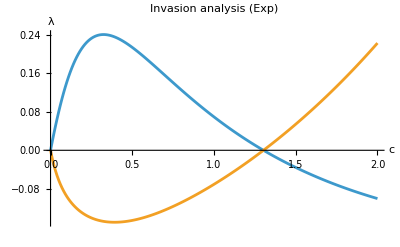

=== Running trade-off analysis for shape: Saturating ===

Optimal parameters: {th→0.799997,v0→0.100004,sj→0.323837,ss→5.99998,me→0.199999}

λ_max = 0.0446918

Optimal care level (c*) = 0.2

Resident equilibrium A = 100.

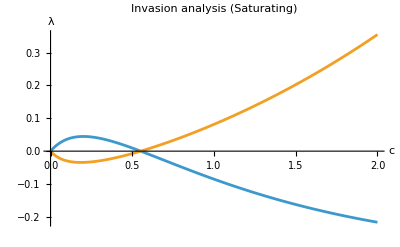

=== Running trade-off analysis for shape: Sigmoid ===

Optimal parameters: {th→0.8,v0→0.1,sj→0.323823,ss→6.,me→0.2}

λ_max = 0.16343

Optimal care level (c*) = 0.56

Resident equilibrium A = 105.691

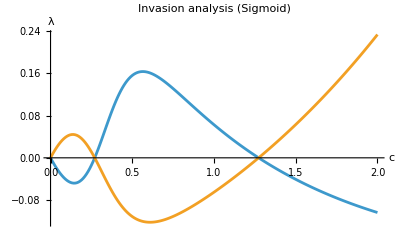

=== Running trade-off analysis for shape: Linear ===

Optimal parameters: {th→0.101307,v0→0.143549,sj→0.662713,ss→5.54832,me→0.199143}

λ_max = 0.

Optimal care level (c*) = 0.

Resident equilibrium A = 123.923

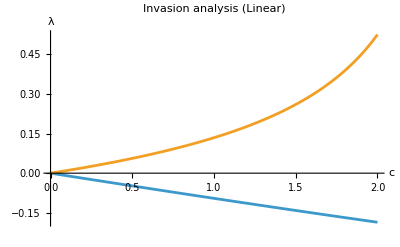

```mathematica
(*Run it for all trade-offs*)
Table[runTradeOffAnalysis[shape,6],{shape,{"Exp","Saturating","Sigmoid","Linear"}}];
```

```mathematica
7
```

7

# Transformed Parameters

```mathematica
baselineExpRev={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,a->6};
baselineLinearRev={θ->0.10130733924210514,ν0->0.14354851056163923,σJ0->0.662712790280335,s->5.548320231688571,mE->0.19914292352304955,K->250,a->6};
baselineSatRev={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,a->6};
baselineSigRev={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,a->6};

cStarExpRev=0.32;
cStarLinRev=0.7;
cStarSatRev=0.2;
cStarSigRev=0.57;

resExpRev=tradeOff["Exp"][baselineExpRev,0];
resLinearRev=tradeOff["Linear"][baselineLinearRev,0];
resSatRev=tradeOff["Saturating"][baselineSatRev,0];
resSigRev=tradeOff["Sigmoid"][baselineSigRev,0];

careExpRev=tradeOff["Exp"][baselineExpRev,cStarExpRev];
careLinearRev=tradeOff["Linear"][baselineLinearRev,cStarLinRev];
careSatRev=tradeOff["Saturating"][baselineSatRev,cStarSatRev];
careSigRev=tradeOff["Sigmoid"][baselineSigRev,cStarSigRev];

Grid[Prepend[{{"Exp",resExpRev[[1]],resExpRev[[2]],resExpRev[[3]],resExpRev[[4]]},{"Sat",resSatRev[[1]],resSatRev[[2]],resSatRev[[3]],resSatRev[[4]]},{"Sig",resSigRev[[1]],resSigRev[[2]],resSigRev[[3]],resSigRev[[4]]}},{Style["Shape",Bold],Style["μ*",Bold],Style["r*",Bold],Style["ν*",Bold],Style["σJ*",Bold]}],Frame->All,BaseStyle->{FontFamily->"Helvetica",FontSize->14},Alignment->Center,Spacings->{1.5,1},ItemSize->All,FrameStyle->Thickness[0.003]]

Grid[Prepend[{{"Exp",careExpRev[[1]],careExpRev[[2]],careExpRev[[3]],careExpRev[[4]]},{"Sat",careSatRev[[1]],careSatRev[[2]],careSatRev[[3]],careSatRev[[4]]},{"Sig",careSigRev[[1]],careSigRev[[2]],careSigRev[[3]],careSigRev[[4]]}},{Style["Shape",Bold],Style["μ(c*)",Bold],Style["r(c*)",Bold],Style["ν(c*)",Bold],Style["σJ(c*)",Bold]}],Frame->All,BaseStyle->{FontFamily->"Helvetica",FontSize->14},Alignment->Center,Spacings->{1.5,1},ItemSize->All,FrameStyle->Thickness[0.003]]
```

Shape | μ* | r* | ν* | σJ*
Exp | 0.8 | 4.91238 | 0.263142 | 0.446393
Sat | 0.8 | 4.91238 | 0.263142 | 0.446393
Sig | 0.762059 | 4.91238 | 0.263142 | 0.446393

Shape | μ(c*) | r(c*) | ν(c*) | σJ(c*)
Exp | 0.117286 | 3.56712 | 0.464932 | 0.918837
Sat | 0.512 | 4.18606 | 0.372091 | 0.627836
Sig | 0.0503787 | 2.77808 | 0.583288 | 0.963402

# Parameters when no - care reinvades

```mathematica
baselineExpRev2={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,a->6};
baselineSatRev2={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,a->6};
baselineSigRev2={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,a->6};

cStarExpRev2=1.31;
cStarSatRev2=0.55;
cStarSigRev2=1.27;

resExpRev2=tradeOff["Exp"][baselineExpRev2,0];
resSatRev2=tradeOff["Saturating"][baselineSatRev2,0];
resSigRev2=tradeOff["Sigmoid"][baselineSigRev2,0];

careExpRev2=tradeOff["Exp"][baselineExpRev2,cStarExpRev2];
careSatRev2=tradeOff["Saturating"][baselineSatRev2,cStarSatRev2];
careSigRev2=tradeOff["Sigmoid"][baselineSigRev2,cStarSigRev2];

Grid[Prepend[{{"Exp",resExpRev2[[1]],resExpRev2[[2]],resExpRev2[[3]],resExpRev2[[4]]},{"Sat",resSatRev2[[1]],resSatRev2[[2]],resSatRev2[[3]],resSatRev2[[4]]},{"Sig",resSigRev2[[1]],resSigRev2[[2]],resSigRev2[[3]],resSigRev2[[4]]}},{Style["Shape",Bold],Style["μ*",Bold],Style["r*",Bold],Style["ν*",Bold],Style["σJ*",Bold]}],Frame->All,BaseStyle->{FontFamily->"Helvetica",FontSize->14},Alignment->Center,Spacings->{1.5,1},ItemSize->All,FrameStyle->Thickness[0.003]]

Grid[Prepend[{{"Exp",careExpRev2[[1]],careExpRev2[[2]],careExpRev2[[3]],careExpRev2[[4]]},{"Sat",careSatRev2[[1]],careSatRev2[[2]],careSatRev2[[3]],careSatRev2[[4]]},{"Sig",careSigRev2[[1]],careSigRev2[[2]],careSigRev2[[3]],careSigRev2[[4]]}},{Style["Shape",Bold],Style["μ(c*)",Bold],Style["r(c*)",Bold],Style["ν(c*)",Bold],Style["σJ(c*)",Bold]}],Frame->All,BaseStyle->{FontFamily->"Helvetica",FontSize->14},Alignment->Center,Spacings->{1.5,1},ItemSize->All,FrameStyle->Thickness[0.003]]
```

Shape | μ* | r* | ν* | σJ*
Exp | 0.8 | 4.91238 | 0.263142 | 0.446393
Sat | 0.8 | 4.91238 | 0.263142 | 0.446393
Sig | 0.762059 | 4.91238 | 0.263142 | 0.446393

Shape | μ(c*) | r(c*) | ν(c*) | σJ(c*)
Exp | 0.000308699 | 1.32546 | 0.801181 | 0.999786
Sat | 0.334118 | 3.16375 | 0.525437 | 0.739903
Sig | 0.0000490238 | 1.37955 | 0.793067 | 0.999964

# Plot how care changes the optimal parameters

```mathematica
params={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,a->6};

shapes={"Saturating","Sigmoid","Exp"};
colors={Purple,Red, Blue};
labels={"μ(c)","r(c)","ν(c)","σJ(c)"};

cmin=0;cmax=2;


trait[shape_,i_,c_]:=tradeOff[shape][params,c][[i]];


plots=Table[Plot[Evaluate@Table[trait[shape,i,c],{shape,shapes}],{c,cmin,cmax},PlotStyle->Thread[{colors,Thick}],PlotLegends->shapes,PlotRange->All,AxesLabel->{"c",labels[[i]]},PlotLabel->labels[[i]],ImageSize->450],{i,1,4}];

GraphicsGrid[Partition[plots,2],Spacings->{0.5,0.8}]
```

-Graphics-

## Just plotting exponential

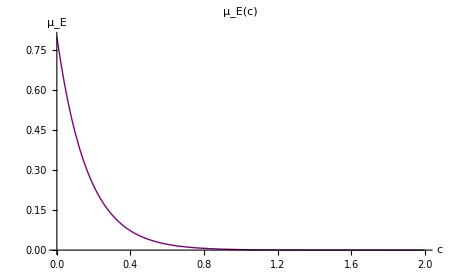

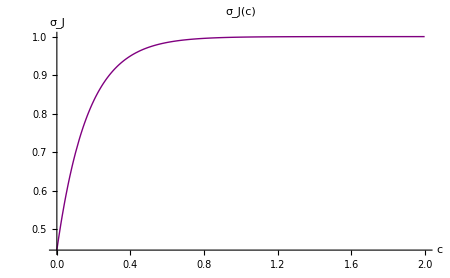

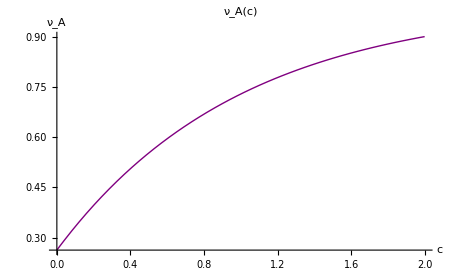

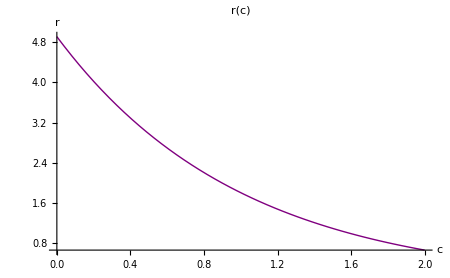

```mathematica
params={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,a->6};



plotMuE=Plot[tradeOff["Exp"][params,c][[1]],{c,0,2},PlotStyle->Directive[Purple,Thick],PlotRange->All,AxesLabel->{"c",Subscript[μ,"E"]},PlotLabel->Style[Row[{Subscript[μ,"E"],"(c)"}],16],ImageSize->450,TicksStyle->Directive[Black,12],LabelStyle->Directive[Black,14],PlotTheme->"Classic"];


plotSigmaJ=Plot[tradeOff["Exp"][params,c][[4]],{c,0,2},PlotStyle->Directive[Purple,Thick],PlotRange->All,AxesLabel->{"c",Subscript[σ,"J"]},PlotLabel->Style[Row[{Subscript[σ,"J"],"(c)"}],16],ImageSize->450,TicksStyle->Directive[Black,12],LabelStyle->Directive[Black,14],PlotTheme->"Classic"];

plotNuA=Plot[tradeOff["Exp"][params,c][[3]],{c,0,2},PlotStyle->Directive[Purple,Thick],PlotRange->All,AxesLabel->{"c",Subscript[ν,"A"]},PlotLabel->Style[Row[{Subscript[ν,"A"],"(c)"}],16],ImageSize->450,TicksStyle->Directive[Black,12],LabelStyle->Directive[Black,14],PlotTheme->"Classic"];


plotR=Plot[tradeOff["Exp"][params,c][[2]],{c,0,2},PlotStyle->Directive[Purple,Thick],PlotRange->All,AxesLabel->{"c","r"},PlotLabel->Style["r(c)",16],ImageSize->450,TicksStyle->Directive[Black,12],LabelStyle->Directive[Black,14],PlotTheme->"Classic"];


plotMuE
plotSigmaJ
plotNuA
plotR
```

## Version for Appendix

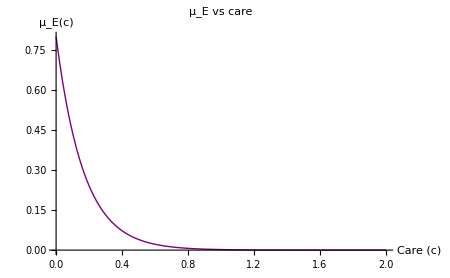

```mathematica
Plot[tradeOff["Exp"][params,c][[1]],{c,0,2},PlotStyle->Directive[Purple,Thick],PlotRange->All,AxesLabel->{"Care (c)",Row[{Subscript[μ,"E"],"(c)"}]},PlotLabel->Row[{Subscript[μ,"E"]," vs care"}],ImageSize->450]
```

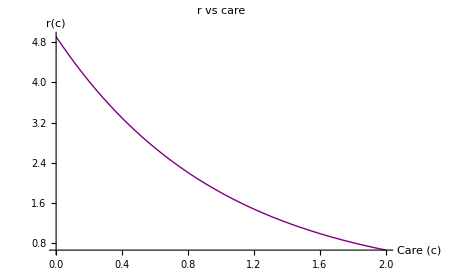

-Graphics-

```mathematica
Plot[tradeOff["Exp"][params,c][[2]],{c,0,2},PlotStyle->Directive[Purple,Thick],PlotRange->All,AxesLabel->{"Care (c)","r(c)"},PlotLabel->"r vs care",ImageSize->450]
```

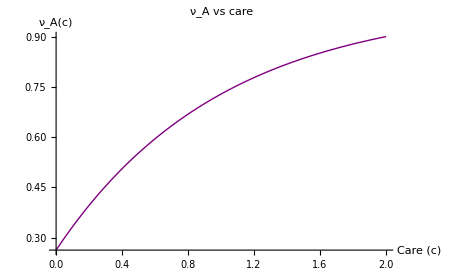

```mathematica
Plot[tradeOff["Exp"][params,c][[3]],{c,0,2},PlotStyle->Directive[Purple,Thick],PlotRange->All,AxesLabel->{"Care (c)",Row[{Subscript[ν,"A"],"(c)"}]},PlotLabel->Row[{Subscript[ν,"A"]," vs care"}],ImageSize->450]
```

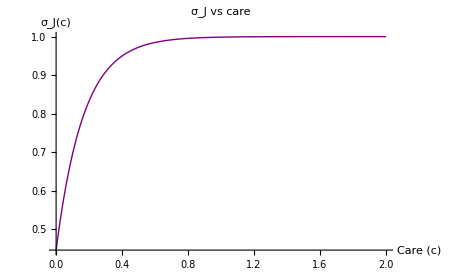

```mathematica
Plot[tradeOff["Exp"][params,c][[4]],{c,0,2},PlotStyle->Directive[Purple,Thick],PlotRange->All,AxesLabel->{"Care (c)",Row[{Subscript[σ,"J"],"(c)"}]},PlotLabel->Row[{Subscript[σ,"J"]," vs care"}],ImageSize->450]
```

## Plots including linear

```mathematica
params2={θ->0.8,ν0->0.1,σJ0->0.323,s->6,a->6,mE->0.2,K->250};

shapes2={"Exp","Saturating","Sigmoid", "Linear"};
labels={"μ(c)","r(c)","ν(c)","σJ(c)"};
colors2={Blue,Purple, Red, Green};  

traitVal2[shape_,i_,c_]:=tradeOff[shape][params2,c][[i]];

plots2=Table[Plot[Evaluate@Table[traitVal2[shape,i,c],{shape,shapes2}],{c,0,2},PlotStyle->Thread[{colors2,Thick}],PlotLegends->shapes2,AxesLabel->{"c",labels[[i]]},PlotRange->All,PlotLabel->labels[[i]],ImageSize->450],{i,1,4}];

GraphicsGrid[Partition[plots2,2],Spacings->{0.7,0.7}]
```

-Graphics-

-Graphics-

# Plots in more detail for figures

## Exponential

Exponential — optimal care = {0.32,0.24}

Exponential — crossing c = 1.305 -> λ = 0.00061795

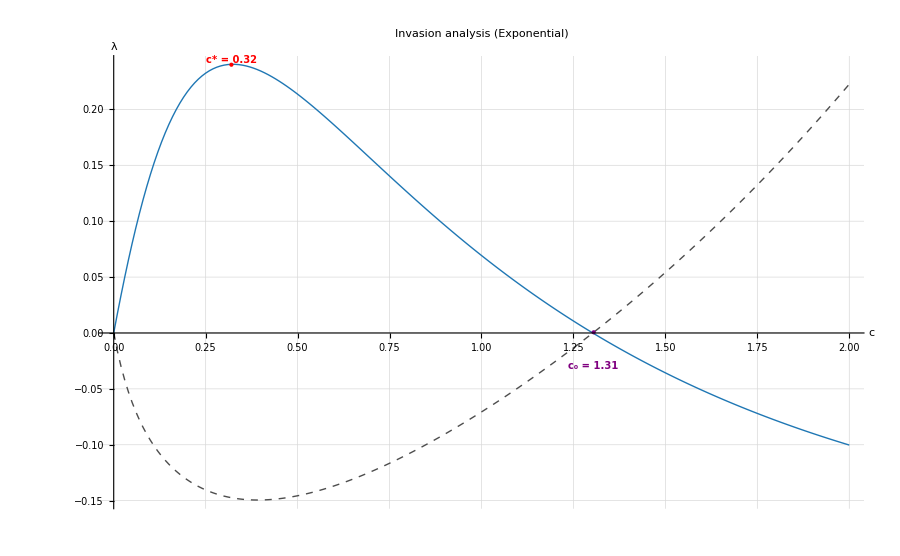

```mathematica
paramsExp={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,K->250,a->6};


fitCareExp=getFit[paramsExp,"Exp"];          
fitNoCareExp=getFlippedFit[paramsExp,"Exp"];   


colCare=RGBColor[0.121,0.467,0.705];
colNoCare=GrayLevel[0.3];  


plotStyleExp={Directive[colCare,Thick],Directive[colNoCare,Thick,Dashed]};

interpCareExp=Interpolation[fitCareExp];
interpNoCareExp=Interpolation[fitNoCareExp];


dotMax={0.32,0.24};   
cCrossExp=1.305;       


yCrossExp=Quiet@Check[interpNoCareExp[cCrossExp],Indeterminate];


Print["Exponential — optimal care = ",dotMax];
Print["Exponential — crossing c = ",cCrossExp," -> λ = ",yCrossExp];

plotExpHardDots=ListLinePlot[{fitCareExp,fitNoCareExp},PlotStyle->plotStyleExp,Joined->True,PlotRange->All,AxesLabel->{"c","λ"},PlotLabel->"Invasion analysis (Exponential)",GridLines->Automatic,PlotRangePadding->Scaled[0.03],ImagePadding->{{60,110},{50,60}},Epilog->{Red,PointSize[Large],Point[dotMax],Text[Style[Row[{"c* = ",NumberForm[dotMax[[1]],{3,2}]}],10,Bold,Red],dotMax,{0.2,-1.5}],Purple,PointSize[Large],Point[{cCrossExp,yCrossExp}],Text[Style[Row[{Subscript[c,0]," = ",NumberForm[cCrossExp,{3,2}]}],10,Bold,Purple],{cCrossExp,yCrossExp-0.03}],Inset[Graphics[{{AbsoluteThickness[3],colCare,Line[{{0,0.2},{0.4,0.2}}]},{Black,Text[Style["Care invading no-care",10],{1,0.2}]},{AbsoluteThickness[3],colNoCare,Dashed,Line[{{0,-0.2},{0.4,-0.2}}]},{Black,Text[Style["No-care invading care",10],{1,-0.2}]}},PlotRange->{{0,1.6},{-0.9,0.4}},ImageSize->160],Scaled[{0.78,0.78}]]},ImageSize->900];


plotExpHardDots
```

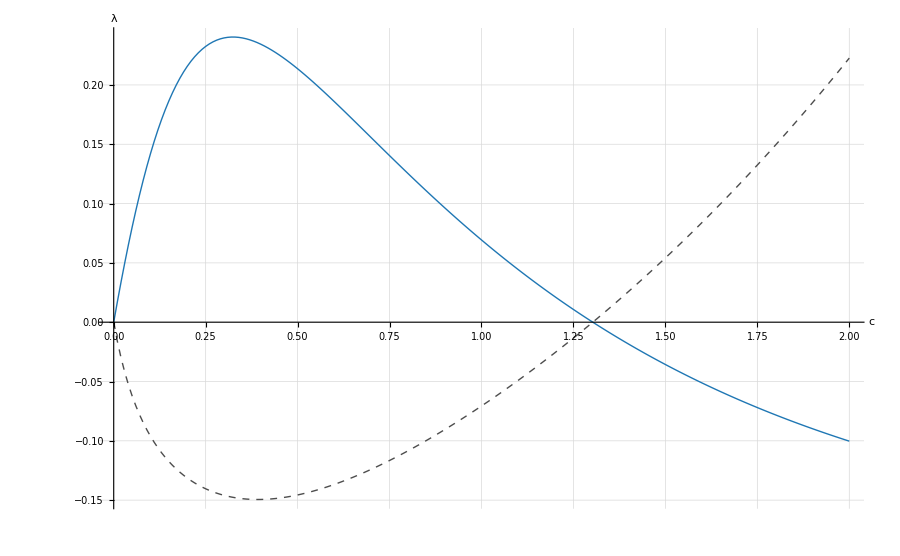

```mathematica
paramsExp={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,K->250,a->6};

fitCareExp=getFit[paramsExp,"Exp"];
fitNoCareExp=getFlippedFit[paramsExp,"Exp"];

colCare=RGBColor[0.121,0.467,0.705];
colNoCare=GrayLevel[0.3];

plotStyleExp={Directive[colCare,Thick],Directive[colNoCare,Thick,Dashed]};

plotExpClean=ListLinePlot[{fitCareExp,fitNoCareExp},PlotStyle->plotStyleExp,Joined->True,PlotRange->All,AxesLabel->{"c","λ"},GridLines->Automatic,PlotRangePadding->Scaled[0.03],ImagePadding->{{60,110},{50,60}},PlotLegends->Placed[LineLegend[{colCare,Directive[colNoCare,Dashed]},{"Care invading no-care","No-care invading care"},LabelStyle->{FontFamily->"Times New Roman",12}],{0.72,0.78}  ],ImageSize->900];

plotExpClean
```

```mathematica
paramsExp={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,K->250,a->6};

fitCareExp=getFit[paramsExp,"Exp"];
fitNoCareExp=getFlippedFit[paramsExp,"Exp"];

colCare=RGBColor[0.121,0.467,0.705];
colNoCare=GrayLevel[0.3];

plotStyleExp={Directive[colCare,Thick],Directive[colNoCare,Thick,Dashed]};

plotExpClean=ListLinePlot[{fitCareExp,fitNoCareExp},PlotStyle->plotStyleExp,Joined->True,PlotRange->All,AxesLabel->{Style["c",18],Style["λ",18]},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],GridLines->Automatic,PlotRangePadding->Scaled[0.03],ImagePadding->{{60,110},{50,60}},ImageSize->900];

figureLegendExp=LineLegend[{Directive[colCare,Thick],Directive[colNoCare,Thick,Dashed]},{"Care invading no-care","No-care invading care"},LabelStyle->Directive[14,FontFamily->"Times New Roman"],LegendLayout->"Row"];

plotExpFinal=GraphicsColumn[{figureLegendExp,plotExpClean},Spacings->0.6,Alignment->Center];

plotExpFinal
```

-Graphics-

## Sigmoid

Sigmoid — c* = 0.56 -> λ = 0.16343

Sigmoid — crossing 1 c = 0.27 -> λ = 0.000113137

Sigmoid — crossing 2 c = 1.275 -> λ = 0.000510006

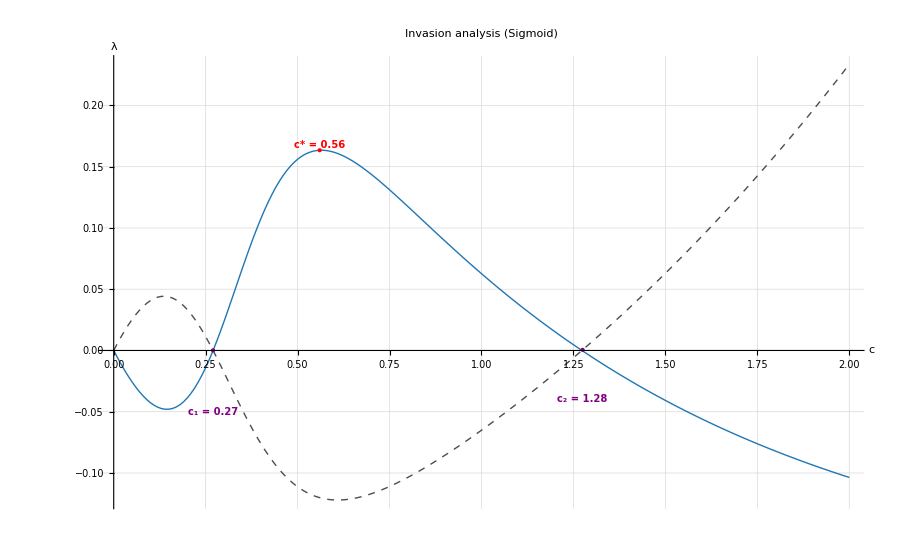

```mathematica
paramsSig={θ->0.8,ν0->0.1,σJ0->0.323823,s->6,mE->0.2,K->250,a->6};

fitCareSig=getFit[paramsSig,"Sigmoid"];
fitNoCareSig=getFlippedFit[paramsSig,"Sigmoid"];


colCare=RGBColor[0.121,0.467,0.705];
colNoCare=GrayLevel[0.3];   

plotStyleSig={Directive[colCare,Thick],Directive[colNoCare,Thick,Dashed]};


interpCareSig=Interpolation[fitCareSig];
interpNoCareSig=Interpolation[fitNoCareSig];

cStarSig=0.56;
cCross1=0.27;
cCross2=1.275;

yStarSig=Quiet@Check[interpCareSig[cStarSig],Indeterminate];
yCross1=Quiet@Check[interpNoCareSig[cCross1],Indeterminate];
yCross2=Quiet@Check[interpNoCareSig[cCross2],Indeterminate];


Print["Sigmoid — c* = ",cStarSig," -> λ = ",yStarSig];
Print["Sigmoid — crossing 1 c = ",cCross1," -> λ = ",yCross1];
Print["Sigmoid — crossing 2 c = ",cCross2," -> λ = ",yCross2];


plotSigHardDots=ListLinePlot[{fitCareSig,fitNoCareSig},PlotStyle->plotStyleSig,Joined->True,PlotRange->All,AxesLabel->{"c","λ"},PlotLabel->"Invasion analysis (Sigmoid)",GridLines->Automatic,PlotRangePadding->Scaled[0.03],ImagePadding->{{60,110},{50,60}},Epilog->{Red,PointSize[Large],Point[{cStarSig,yStarSig}],Text[Style[Row[{"c* = ",NumberForm[cStarSig,{3,2}]}],10,Bold,Red],{cStarSig,yStarSig},{0.2,-1.5}],Purple,PointSize[Large],Point[{cCross1,yCross1}],Text[Style[Row[{Subscript[c,1]," = ",NumberForm[cCross1,{3,2}]}],10,Bold,Purple],{cCross1,yCross1-0.05}],Purple,PointSize[Large],Point[{cCross2,yCross2}],Text[Style[Row[{Subscript[c,2]," = ",NumberForm[cCross2,{3,2}]}],10,Bold,Purple],{cCross2,yCross2-0.04}],Inset[Graphics[{{AbsoluteThickness[3],colCare,Line[{{0,0.2},{0.4,0.2}}]},{Black,Text[Style["Care invading no-care",10],{1,0.2}]},{AbsoluteThickness[3],colNoCare,Dashed,Line[{{0,-0.2},{0.4,-0.2}}]},{Black,Text[Style["No-care invading care",10],{1,-0.2}]}},PlotRange->{{0,1.6},{-0.9,0.4}},ImageSize->160],Scaled[{0.78,0.78}]]},ImageSize->900];

plotSigHardDots
```

## Saturating

Saturating (exact params) — c* = 0.2 -> λ = 0.0446913

Saturating (exact params) — crossing c = 0.55 -> λ = -0.000190001

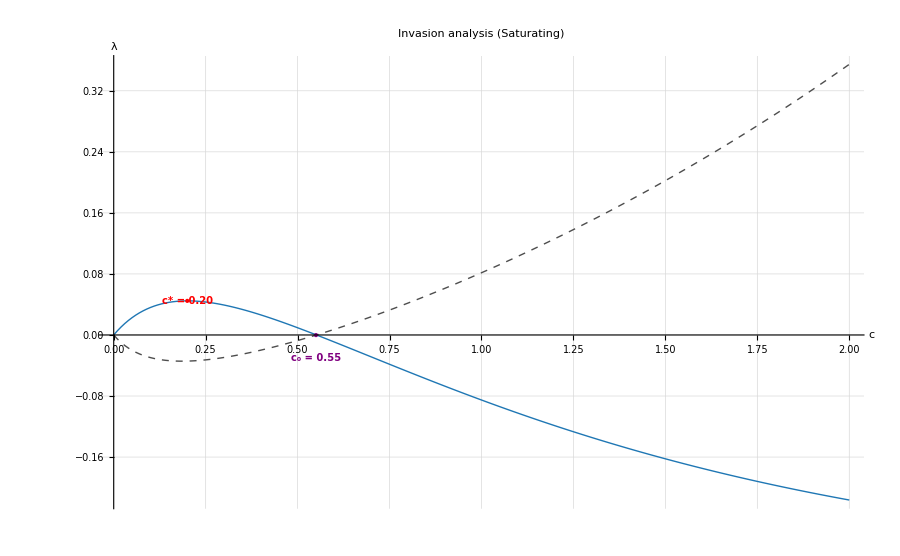

```mathematica
paramsSat={θ->0.79999997,ν0->0.100004,σJ0->0.323837,s->5.99998,mE->0.1999999,K->250,a->6};

fitCareSat=getFit[paramsSat,"Saturating"];
fitNoCareSat=getFlippedFit[paramsSat,"Saturating"];


colCare=RGBColor[0.121,0.467,0.705];
colNoCare=GrayLevel[0.3];   

plotStyleSat={Directive[colCare,Thick],Directive[colNoCare,Thick,Dashed]};


interpCareSat=Interpolation[fitCareSat];
interpNoCareSat=Interpolation[fitNoCareSat];


cStarSat=0.2;
cCrossSat=0.55;

yStarSat=Quiet@Check[interpCareSat[cStarSat],Indeterminate];
yCrossSat=Quiet@Check[interpNoCareSat[cCrossSat],Indeterminate];


Print["Saturating (exact params) — c* = ",cStarSat," -> λ = ",yStarSat];
Print["Saturating (exact params) — crossing c = ",cCrossSat," -> λ = ",yCrossSat];


plotSatHardDots=ListLinePlot[{fitCareSat,fitNoCareSat},PlotStyle->plotStyleSat,Joined->True,PlotRange->All,AxesLabel->{"c","λ"},PlotLabel->"Invasion analysis (Saturating)",GridLines->Automatic,PlotRangePadding->Scaled[0.03],ImagePadding->{{60,110},{50,60}},Epilog->{Red,PointSize[Large],Point[{cStarSat,yStarSat}],Text[Style[Row[{"c* = ",NumberForm[cStarSat,{3,2}]}],10,Bold,Red],{cStarSat,yStarSat},{0,-3}],Purple,PointSize[Large],Point[{cCrossSat,yCrossSat}],Text[Style[Row[{Subscript[c,0]," = ",NumberForm[cCrossSat,{3,2}]}],10,Bold,Purple],{cCrossSat,yCrossSat-0.03}],Inset[Graphics[{{AbsoluteThickness[3],colCare,Line[{{0,0.2},{0.4,0.2}}]},{Black,Text[Style["Care invading no-care",10],{1,0.2}]},{AbsoluteThickness[3],colNoCare,Dashed,Line[{{0,-0.2},{0.4,-0.2}}]},{Black,Text[Style["No-care invading care",10],{1,-0.2}]}},PlotRange->{{0,1.6},{-0.9,0.4}},ImageSize->160],Scaled[{0.78,0.5}]]},ImageSize->900];

plotSatHardDots
```

## Linear

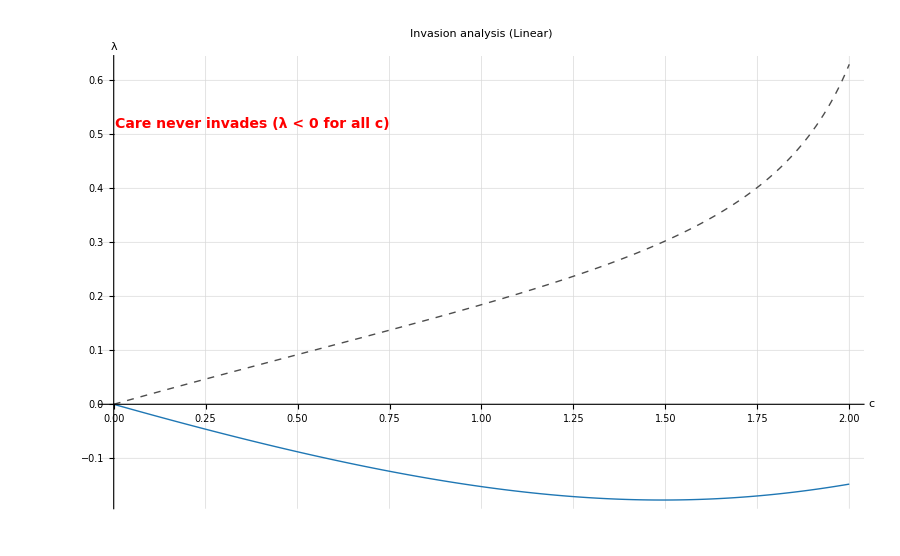

```mathematica
paramsLin={θ->0.77755,ν0->0.205762,σJ0->0.758399,s->5.98999,mE->0.15005,K->250,a->6};

fitCareLin=getFit[paramsLin,"Linear"];
fitNoCareLin=getFlippedFit[paramsLin,"Linear"];


colCare=RGBColor[0.121,0.467,0.705];
colNoCare=GrayLevel[0.3];   

plotStyleLin={Directive[colCare,Thick],Directive[colNoCare,Thick,Dashed]};


plotLin=ListLinePlot[{fitCareLin,fitNoCareLin},PlotStyle->plotStyleLin,Joined->True,PlotRange->All,AxesLabel->{"c","λ"},PlotLabel->"Invasion analysis (Linear)",GridLines->Automatic,PlotRangePadding->Scaled[0.03],ImagePadding->{{60,110},{90,60}},Epilog->{Inset[Style["Care never invades (λ < 0 for all c)",14,Bold,Red],Scaled[{0.2,0.85}]],Inset[Graphics[{{AbsoluteThickness[3],colCare,Line[{{0,0.2},{0.4,0.2}}]},{Black,Text[Style["Care invading no-care",10],{1,0.2}]},{AbsoluteThickness[3],colNoCare,Dashed,Line[{{0,-0.2},{0.4,-0.2}}]},{Black,Text[Style["No-care invading care",10],{1,-0.2}]}},PlotRange->{{0,1.6},{-0.9,0.4}},ImageSize->160],Scaled[{0.78,0.78}]]},ImageSize->900];

plotLin
```